R. Pure, S. Durrani, F. Tong and J. Pan, “Distance Distribution Between Two Random Nodes in Arbitrary Polygons,” Mathematical Methods in Applied Sciences, March 2020 (revised Jan. 2021)
Copyright: R. Pure and S. Durrani, 2021.
Tested in Mathematica 11 and 12

```mathematica
(*PolygonArea computes the area of a polygon using the Shoelace Formula*)PolygonArea[P_]:=1/2 Total[Det/@Partition[Append[P,First@P],2,1]]
(*RandomPointsTriangle generates uniformly random points in a triangle*)
RandomPointsTriangle[{a_,b_,c_},n_]:=Module[{u,v},{u,v}=Transpose[Sort/@RandomReal[1,{n,2}]];
Map[# a&,u]+Map[# b&,(v-u)]+Map[# c&,(1-v)]]
```

```mathematica
(*RandomPointsPolygon generates uniformly random points in a polygon*)
RandomPointsPolygon[P_,n_]:=Module[{p,s,t},p=N[P];(*Numerically approximate vertices for faster computation.*)s=First/@MeshPrimitives[TriangulateMesh[DiscretizeGraphics@Graphics[Polygon@p],MaxCellMeasure->Infinity],2];
t=Accumulate[PolygonArea[#]/PolygonArea[p]&/@s];
(*Triangulate the polygon.Calculate the area of the polygon.Associate each triangle with its fraction of area of the polygon.Associate each triangle with a range calculated as the sum of all previous area fractions.This allows a triangle to be picked from a random variable generated between 0 and 1.*)Select[Map[Function[x,Flatten@RandomPointsTriangle[s[[First@FirstPosition[x<#&/@t,True]]],1]],RandomReal[1,n]],#≠{}&]
(*Random points:Generate n random numbers between 0 and 1. For each random number,pick the corresponding triangle and generate a point in it.*)]
```

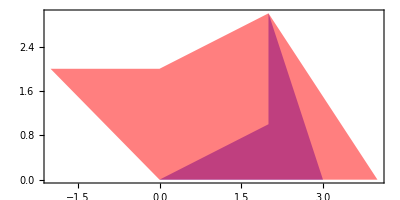

```mathematica
Poly1={{0,0},{3,0},{2,3},{2,1}};
(*Poly2={{3,4},{7,4},{5,7},{3,6},{1,6}}; *)
(*Poly2={{3,1},{7,1},{5,4},{3,3},{1,3}}; *)
Poly2={{0,0},{4,0},{2,3},{0,2},{-2,2}};
pic1=Graphics[{Opacity[0.5],Blue,Polygon[Poly1]}];
pic2=Graphics[{Opacity[0.5], Red,Polygon[Poly2]}];
Show[pic1, pic2, PlotRange->Automatic, Frame->True]
```

```mathematica
n=10000;
data1=RandomPointsPolygon[Poly1,n];
data2=RandomPointsPolygon[Poly2,n];data=Norm[#[[1]]-#[[2]]]&/@Tuples[{data1,data2}];
dist=SmoothKernelDistribution@data;
min=Min@data;
max=Max@data;
```

```mathematica
areatest[r_,θ_]:=Area[RegionIntersection@@Polygon/@{N[#+{r Cos[θ],r Sin[θ]}]&/@Poly1,N/@Poly2}]
```

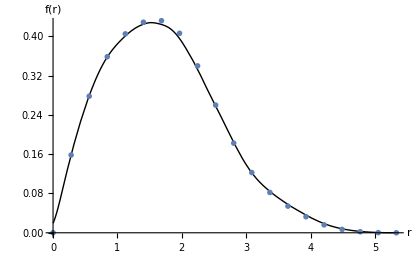

```mathematica
pts=19;(*Number of theoretical PDF points to evaluate: 20 points takes about a minute*)
divs=200;
t=Table[{r,(2 π r)/(divs (Area@Polygon@Poly1) (Area@Polygon@Poly2)) Total@Table[areatest[r,θ],{θ,0,2 π,(2 π)/divs}]},{r,min,max,(max-min)/pts}];
Show[Plot[PDF[dist,x],{x,min,max},PlotStyle->{Black,Thick},PlotLegends->Placed[{"Simulated PDF"},{0.85,0.82}]],ListPlot[t,PlotMarkers->Style["X",{Red,FontSize->15}],PlotLegends->Placed[{"Theoretical PDF"},{0.85,0.82}]],AxesLabel->{"r","f(r)"},LabelStyle->Directive[Bold,20],TicksStyle->Directive[Plain,15]]
```